```mathematica
description="G G -> H A, EW, total decay rate, 1-loop";
If[$FrontEnd===Null,$FeynCalcStartupMessages=False;
Print[description];];
If[$Notebooks===False,$FeynCalcStartupMessages=False];
$LoadAddOns={"FeynArts"};
<<FeynCalc`
$FAVerbose=0;

FCCheckVersion[9,3,1];
```

FeynCalc 10.1.0 (stable version). For help, use the online documentation, visit the forum and have a look at the supplied examples. The PDF-version of the manual can be downloaded here.

If you use FeynCalc in your research, please evaluate FeynCalcHowToCite[] to learn how to cite this software.

Please keep in mind that the proper academic attribution of our work is crucial to ensure the future development of this package!

FeynArts 3.12 (24 May 2024) patched for use with FeynCalc, for documentation see the manual or visit www.feynarts.de.

If you use FeynArts in your research, please cite

• T. Hahn, Comput. Phys. Commun., 140, 418-431, 2001, arXiv:hep-ph/0012260

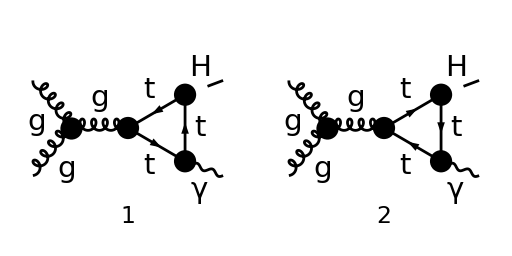

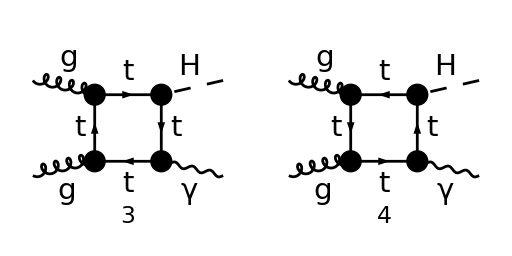

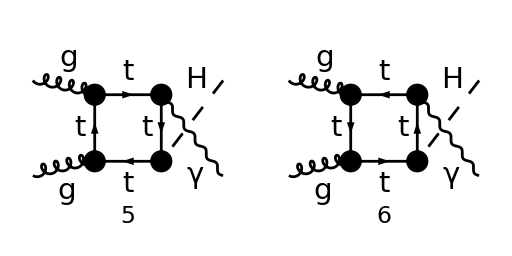

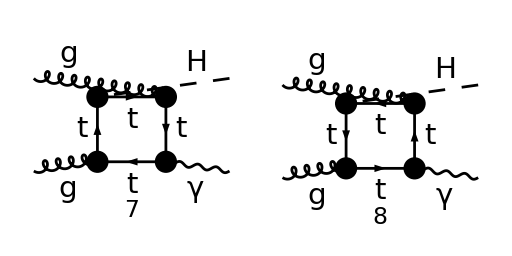

```mathematica
diags=InsertFields[CreateTopologies[1,2->2],{V[5],V[5]}-> {S[1], V[1]},InsertionLevel->{Particles},Model->"SMQCD", ExcludeParticles->{F[4],F[3,{1}],F[3,{2}]}];

Paint[diags,ColumnsXRows->{2,1},Numbering->Simple,SheetHeader->None,ImageSize->{512,256}];
```

```mathematica
amp[0]=FCFAConvert[CreateFeynAmp[diags,PreFactor->-1],IncomingMomenta->{p1,p2},OutgoingMomenta->{p3,p4},LoopMomenta->{k},List->False,Contract->True,TransversePolarizationVectors->{p1,p2,p4},ChangeDimension->D,DropSumOver->True,SMP->True,UndoChiralSplittings->True]
```

FCFAConvert::sumOverWarn: You are omitting SumOver objects that may represent a nontrivial summation. This may lead to a loss of overall factors multiplying some of your diagrams. Please make sure that this is really what you want.

(tr(-((γ·(k+p2-p3-p4)+m_t).(γ·ε^*(p4)).(γ·(k+p2-p3)+m_t).(γ·(k+p2)+m_t).(γ·ε(p2)).(γ·k+m_t).(γ·ε(p1)) e^2 g_s^2 m_t T_Col6Col5^Glu1 T_Col5Col6^Glu2)/(3 m_W (sin(θ_W)))))/((k^2-m_t^2).((k+p2)^2-m_t^2).((k+p2-p3)^2-m_t^2).((k+p2-p3-p4)^2-m_t^2))+(tr(((γ·(k+p2-p3-p4)+m_t).(γ·ε^*(p4)).(γ·(k+p2-p3)+m_t).(γ·(k+p2)+m_t).(γ·ε(p2)).(γ·k+m_t).(γ·ε(p1)) e^2 g_s^2 m_t T_Col5Col6^Glu1 T_Col6Col5^Glu2)/(3 m_W (sin(θ_W)))))/((k^2-m_t^2).((k+p2)^2-m_t^2).((k+p2-p3)^2-m_t^2).((k+p2-p3-p4)^2-m_t^2))+(tr(((m_t-γ·k).(γ·ε(p2)).(γ·(-k-p2)+m_t).(γ·ε^*(p4)).(γ·(-k-p2+p4)+m_t).(γ·(-k-p2+p3+p4)+m_t).(γ·ε(p1)) e^2 g_s^2 m_t T_Col6Col5^Glu1 T_Col5Col6^Glu2)/(3 m_W (sin(θ_W)))))/((k^2-m_t^2).((k+p2)^2-m_t^2).((k+p2-p4)^2-m_t^2).((k+p2-p3-p4)^2-m_t^2))+(tr(-((m_t-γ·k).(γ·ε(p2)).(γ·(-k-p2)+m_t).(γ·ε^*(p4)).(γ·(-k-p2+p4)+m_t).(γ·(-k-p2+p3+p4)+m_t).(γ·ε(p1)) e^2 g_s^2 m_t T_Col5Col6^Glu1 T_Col6Col5^Glu2)/(3 m_W (sin(θ_W)))))/((k^2-m_t^2).((k+p2)^2-m_t^2).((k+p2-p4)^2-m_t^2).((k+p2-p3-p4)^2-m_t^2))+(tr(-((γ·(k+p2-p3-p4)+m_t).(γ·ε^*(p4)).(γ·(k+p2-p3)+m_t).(γ·ε(p2)).(γ·(k-p3)+m_t).(γ·k+m_t).(γ·ε(p1)) e^2 g_s^2 m_t T_Col6Col5^Glu1 T_Col5Col6^Glu2)/(3 m_W (sin(θ_W)))))/((k^2-m_t^2).((k-p3)^2-m_t^2).((k+p2-p3)^2-m_t^2).((k+p2-p3-p4)^2-m_t^2))+(tr(((γ·(k+p2-p3-p4)+m_t).(γ·ε^*(p4)).(γ·(k+p2-p3)+m_t).(γ·ε(p2)).(γ·(k-p3)+m_t).(γ·k+m_t).(γ·ε(p1)) e^2 g_s^2 m_t T_Col5Col6^Glu1 T_Col6Col5^Glu2)/(3 m_W (sin(θ_W)))))/((k^2-m_t^2).((k-p3)^2-m_t^2).((k+p2-p3)^2-m_t^2).((k+p2-p3-p4)^2-m_t^2))-(tr((γ·(k+p3)+m_t).0.(γ·(k-p4)+m_t).(-2/3 ⅈ γ^Lor3 e).(γ·k+m_t).(-(ⅈ e m_t)/(2 m_W (sin(θ_W))))) (-p2-p3-p4)^Lor1 ε^Lor1(p1) g^Lor2Lor4 ε^Lor2(p2) (ε^*)^Lor3(p4) g^Lor4Lor5 g_s f^Glu1Glu2Glu5)/((k^2-m_t^2).((k+p3)^2-m_t^2).((k-p4)^2-m_t^2) (p3+p4)^2)-(tr((γ·(k+p3)+m_t).0.(γ·(k-p4)+m_t).(2/3 ⅈ γ^Lor3 e).(γ·k+m_t).(-(ⅈ e m_t)/(2 m_W (sin(θ_W))))) (-p2-p3-p4)^Lor1 ε^Lor1(p1) g^Lor2Lor4 ε^Lor2(p2) (ε^*)^Lor3(p4) g^Lor4Lor5 g_s f^Glu1Glu2Glu5)/((k^2-m_t^2).((k+p3)^2-m_t^2).((k-p4)^2-m_t^2) (p3+p4)^2)-(tr((γ·(k+p3)+m_t).0.(γ·(k-p4)+m_t).(-2/3 ⅈ γ^Lor3 e).(γ·k+m_t).(-(ⅈ e m_t)/(2 m_W (sin(θ_W))))) g^Lor1Lor4 ε^Lor1(p1) (p1+p3+p4)^Lor2 ε^Lor2(p2) (ε^*)^Lor3(p4) g^Lor4Lor5 g_s f^Glu1Glu2Glu5)/((k^2-m_t^2).((k+p3)^2-m_t^2).((k-p4)^2-m_t^2) (p3+p4)^2)-(tr((γ·(k+p3)+m_t).0.(γ·(k-p4)+m_t).(2/3 ⅈ γ^Lor3 e).(γ·k+m_t).(-(ⅈ e m_t)/(2 m_W (sin(θ_W))))) g^Lor1Lor4 ε^Lor1(p1) (p1+p3+p4)^Lor2 ε^Lor2(p2) (ε^*)^Lor3(p4) g^Lor4Lor5 g_s f^Glu1Glu2Glu5)/((k^2-m_t^2).((k+p3)^2-m_t^2).((k-p4)^2-m_t^2) (p3+p4)^2)-(tr((γ·(k+p3)+m_t).0.(γ·(k-p4)+m_t).(-2/3 ⅈ γ^Lor3 e).(γ·k+m_t).(-(ⅈ e m_t)/(2 m_W (sin(θ_W))))) g^Lor1Lor2 ε^Lor1(p1) ε^Lor2(p2) (ε^*)^Lor3(p4) g^Lor4Lor5 (p2-p1)^Lor4 g_s f^Glu1Glu2Glu5)/((k^2-m_t^2).((k+p3)^2-m_t^2).((k-p4)^2-m_t^2) (p3+p4)^2)-(tr((γ·(k+p3)+m_t).0.(γ·(k-p4)+m_t).(2/3 ⅈ γ^Lor3 e).(γ·k+m_t).(-(ⅈ e m_t)/(2 m_W (sin(θ_W))))) g^Lor1Lor2 ε^Lor1(p1) ε^Lor2(p2) (ε^*)^Lor3(p4) g^Lor4Lor5 (p2-p1)^Lor4 g_s f^Glu1Glu2Glu5)/((k^2-m_t^2).((k+p3)^2-m_t^2).((k-p4)^2-m_t^2) (p3+p4)^2)

```mathematica
amp[1]=amp[0]//FCTraceFactor//SUNSimplify
```

0

```mathematica
subamp[0] = FCFAConvert[CreateFeynAmp[DiagramExtract[diags,{3,4}],PreFactor->-1],IncomingMomenta->{p1,p2},OutgoingMomenta->{p3,p4},LoopMomenta->{k},List->False,Contract->True,TransversePolarizationVectors->{p1,p2,p4},ChangeDimension->D,DropSumOver->True,SMP->True,UndoChiralSplittings->True]
```

(tr((e^2 g_s^2 m_t T_Col6Col5^Glu1 T_Col5Col6^Glu2 (m_t-γ·k).(γ·ε(p2)).(γ·(-k-p2)+m_t).(γ·ε^*(p4)).(γ·(-k-p2+p4)+m_t).(γ·(-k-p2+p3+p4)+m_t).(γ·ε(p1)))/(3 m_W (sin(θ_W)))))/((k^2-m_t^2).((k+p2)^2-m_t^2).((k+p2-p4)^2-m_t^2).((k+p2-p3-p4)^2-m_t^2))+(tr(-(e^2 g_s^2 m_t T_Col5Col6^Glu1 T_Col6Col5^Glu2 (m_t-γ·k).(γ·ε(p2)).(γ·(-k-p2)+m_t).(γ·ε^*(p4)).(γ·(-k-p2+p4)+m_t).(γ·(-k-p2+p3+p4)+m_t).(γ·ε(p1)))/(3 m_W (sin(θ_W)))))/((k^2-m_t^2).((k+p2)^2-m_t^2).((k+p2-p4)^2-m_t^2).((k+p2-p3-p4)^2-m_t^2))

```mathematica
subamp[1]=subamp[0]//FCTraceFactor//SUNSimplify
```

0